#### Phase boundary (non-normalized coordinates)

```mathematica
g[T_,P_,x_]:=(9 P)/x-9 x-9 T Log[-1+1/x];
P[T_,x_]:=-(x (T+(-1+x) x))/(-1+x);
T0=T/.Solve[P[T,xl]==P[T,xg],T][[1]];
P0=P[T0,xg];
XGL=(2-xg-xl) (-xg+xl)==(1- xg) (1-xl) (xg+xl) Log[((1- xg) xl)/(xg (1- xl))];
TconstantP1=T/.Solve[P[T,h]==Prs,T]/.h->x;
TconstantP=TconstantP1[[1]];
gas=Table[{xg,P[Tm,xg]}/.xg->Re[xg/.FindRoot[XGL/.NSolve[Tm==T0,xl][[1]],{xg,0.0001}]],{Tm,0.01,8/27,0.001}]//Quiet;
liqxl=Table[Max[xl/.NSolve[gas[[n]][[2]]==P[0.01+(n-1)*0.001,xl]]],{n,1,Length[gas],1}];
liq=Table[{liqxl[[n]],P[0.01+(n-1)*0.001,liqxl[[n]]]},{n,1,Length[gas],1}];
gasT=Table[{gas[[n]][[1]],0.01+(n-1)*0.001},{n,1,Length[gas],1}];
liqT=Table[{liq[[n]][[1]],0.01+(n-1)*0.001},{n,1,Length[liq],1}];
pdT=Union[gasT,liqT];
pdXT=Table[pdT[[n]][[1]],{n,1,Length[pdT]}];
pdYT=Table[pdT[[n]][[2]],{n,1,Length[pdT]}];
pdTxsmooth=ListInterpolation[pdYT,pdXT];
(*Manipulate[
Show[
Plot[pdTxsmooth[x],{x,0.001,1},PlotStyle->{Black}, PlotLegends->{"Phase boundary"}],Plot[TconstantP/.Prs-> Pressure,{x,0,1},PlotStyle->{Red,Thick}],
Plot[2 (-1+t)^2 t,{t,0.001,1},PlotStyle->{Blue,Dashed},PlotLegends->{"Singularity/Spinodal curve"}]
],{Pressure,0.1/27,1.001/27}
]*)
```

Loading xCoba and defining the VDW geometry

```mathematica
<< xAct`xCoba`
$PrePrint = ScreenDollarIndices;
DefManifold[Mvdw,2,IndexRange[a,e]];
DefChart[zx,Mvdw,{1,2},{z[],x[]}];
metricvdw=CTensor[DiagonalMatrix[{3/2 x[],1/(x[] (1-x[])^2)-2 E^z[]}],{-zx,-zx},0];
SetCMetric[metricvdw,zx,SignatureOfMetric->{2,0,0}];
CD=CovDOfMetric[metricvdw];
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.4, {2020,2,16}

CopyRight (C) 2002-2020, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.5, {2020,11,29}

CopyRight (C) 2005-2020, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** DefManifold: Defining manifold Mvdw.

** DefVBundle: Defining vbundle TangentMvdw.

** DefChart: Defining chart zx.

** DefTensor: Defining coordinate scalar z[].

** DefTensor: Defining coordinate scalar x[].

** DefMapping: Defining mapping zx.

** DefMapping: Defining inverse mapping izx.

** DefTensor: Defining mapping differential tensor dizx[-a,izxa].

** DefTensor: Defining mapping differential tensor dzx[-a,zxa].

** DefBasis: Defining basis zx. Coordinated basis.

** DefCovD: Defining parallel derivative PDzx[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDzx[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDzx[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDzx[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDzx[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpzx[a,b].

** DefTensor: Defining antisymmetric -1 density etaDownzx[-a,-b].

Geodesic equation

```mathematica
(*Defining the velocity vector*)
u = CTensor[{uz, ux}, {zx}];

(*Geodesic equations are geod1 and geod2:*)
D2u = u[b] CD[-b][u[a]];
geod1 = (D2u[[0, 1, 1]] == 0 // Expand) /. uz PDzx[{1, -zx}][uz] + ux PDzx[{2, -zx}][uz] -> Z''[t] /. {ux -> X'[t], uz -> Z'[t], z[] -> Z[t], x[] -> X[t]};
geod2 = (D2u[[0, 1, 2]] == 0 // Expand) /. uz PDzx[{1, -zx}][ux] + ux PDzx[{2, -zx}][ux] -> X''[t] /. {ux -> X'[t], uz -> Z'[t], z[] -> Z[t], x[] -> X[t]};
```

All trajectories (single source point)

NDSolve::ndsz: At t == 0.81134, step size is effectively zero; singularity or stiff system suspected.

T vs. x

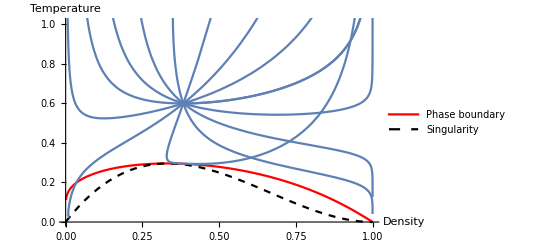

Initial point: (X_0,T_0)=(0.383333,0.6)

Angle range: (Start angle, End angle)=(0,2 π)

Max rays: 15

```mathematica
Clear[solset]
(*Loading package for extracting domain of DE solutions*)
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"]

(*Defining the temperature T*)
T[t_]:=E^(-Z[t]);

(*Setting initial values*)
Subscript[X, 0]=1/3+0.05; (*Initial point of geodesics*)
Subscript[T, 0]=0.6; (*Initial point of geodesics*) (*0.297*)
StartAngle=0;
EndAngle=2π;
Rays=15; (*Number of geodesics from StartAngle to EndAngle*)
tSpan=10;

(*Solving the geodesic equations*)
solset=
Replace[
Reap[
Do[
Sow[
NDSolve[{geod1,geod2,X[0]==Subscript[X, 0],Z[0]==-Log[Subscript[T, 0]],X'[0]==Cos[θ],T'[0]==Sin[θ]},{X,Z},{t,0,tSpan}]
],
{θ,StartAngle,EndAngle,Abs[EndAngle-StartAngle]/(Rays-1)}]][[2,1]],{{x_,y_}}->{x,y},1];

(*Plotting solutions*)
Print["T vs. x"]
Table[ParametricPlot[{X[t]/.solset[[i,1]],E^(-Z[t])/.solset[[i,2]]},{t,0.0001,InterpolatingFunctionDomain[solset[[i,1,2]]][[1,2]]},PlotRange->{{0.325,0.335},{0.295,0.3}}],{i,Length[solset]}];
Prepend[%,Plot[{pdTxsmooth[t],2 (-1+t)^2 t},{t,0.001,1},PlotRange->{{0,1},{0,1.01}},PlotStyle->{Red,{Black,Dashed}},PlotLegends->{"Phase boundary","Singularity"},AxesLabel->{"Density","Temperature"}]];
%//Show
Print["Initial point: (X_0,T_0)=","(",Subscript[X, 0],",",Subscript[T, 0],")" ]
Print["Angle range: (Start angle, End angle)=","(",StartAngle,",",EndAngle,")" ]
Print["Max rays: ", Rays]
```

All trajectories 2 (single source point)*

T vs. x

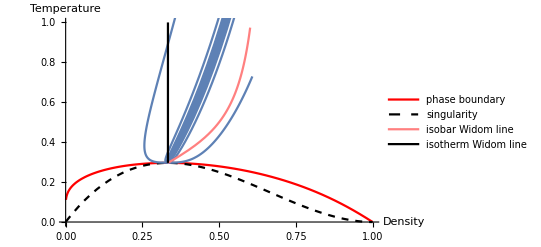

Initial point: (X_0,T_0)=(0.333,0.297)

Angle range: (Start angle, End angle)=(0,π)

Max rays: 20

```mathematica
Clear[solset1]
(*Loading package for extracting domain of DE solutions*)
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"]

(*Defining the temperature T*)
T[t_]:=E^(-Z[t]);

(*Setting initial values*)
Subscript[X, 0]=0.333; (*Initial point of geodesics*)
Subscript[T, 0]=0.297; (*Initial point of geodesics*) (*0.297*)
StartAngle=0;
EndAngle=π;
Rays=20; (*Number of geodesics from StartAngle to EndAngle*)
tSpan=7;

(*Solving the geodesic equations*)
solset1=
Replace[
Reap[
Do[
Sow[
NDSolve[{geod1,geod2,X[0]==Subscript[X, 0],Z[0]==-Log[Subscript[T, 0]],X'[0]==Cos[θ],T'[0]==Sin[θ]},{X,Z},{t,0,tSpan}]
],
{θ,StartAngle,EndAngle,Abs[EndAngle-StartAngle]/(Rays-1)}]][[2,1]],{{x_,y_}}->{x,y},1];

(*Plotting solutions*)
Print["T vs. x"]
Table[ParametricPlot[{X[t]/.solset1[[i,1]],E^(-Z[t])/.solset1[[i,2]]},{t,0.0001,InterpolatingFunctionDomain[solset1[[i,1,2]]][[1,2]]},PlotRange->{{0.325,0.335},{0.295,0.3}}],{i,Length[solset1]}];
Prepend[%,Plot[{pdTxsmooth[t],2 (-1+t)^2 t},{t,0.001,1},PlotRange->{{0,1},{0,1}},PlotStyle->{Red,{Black,Dashed}},PlotLegends->{"phase boundary","singularity"},AxesLabel->{"Density","Temperature"}]];
Append[%,WidomLineSmooth];
Append[%,ParametricPlot[{1/3,t},{t,8/27,1},PlotStyle->{Thick,Black},PlotLegends->{"isotherm Widom line"}]];
%//Show
Print["Initial point: (X_0,T_0)=","(",Subscript[X, 0],",",Subscript[T, 0],")" ]
Print["Angle range: (Start angle, End angle)=","(",StartAngle,",",EndAngle,")" ]
Print["Max rays: ", Rays]
```

Trajectories excluding singularity-bound curves (single source point)

```mathematica
Clear[solset]
(*Loading package for extracting domain of DE solutions*)
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"]

(*Defining the temperature T*)
T[t_]:=E^(-Z[t]);

(*Setting initial values*)
Subscript[X, 0]=0.01; (*Initial point of geodesics*)
Subscript[T, 0]=pdTxsmooth[Subscript[X, 0]]; (*Initial point of geodesics*)
StartAngle=-π;
EndAngle=π/2;
Rays=100; (*Number of geodesics from StartAngle to EndAngle*)

(*Solving the geodesic equations*)
solset=
DeleteCases[
Replace[
Reap[
Do[
Sow[
Catch[
NDSolve[{geod1,geod2,X[0]==Subscript[X, 0],Z[0]==-Log[Subscript[T, 0]],X'[0]==Cos[θ],T'[0]==Sin[θ]},{X,Z},{t,0,3},Method->{"EventLocator","Event":>Abs[X'[t]]>100||Abs[Z'[t]]>100,"EventAction":> Throw[Null,"Reject"]}],
"Reject"]],
{θ,StartAngle,EndAngle,Abs[EndAngle-StartAngle]/Rays}]][[2,1]],{{x_,y_}}->{x,y},1],Null];

(*Plotting solutions*)
Print["T vs. x"]
Table[ParametricPlot[{X[t]/.solset[[i,1]],E^(-Z[t])/.solset[[i,2]]},{t,0.0001,3},PlotRange->{{0,1},{0,1.5}}],{i,Length[solset]}];
Append[%,Plot[{pdTxsmooth[t],2 (-1+t)^2 t},{t,0.001,1},PlotRange->{{0,1},{0,0.6}},PlotStyle->{Red,{Black,Dashed}},PlotLegends->{"Phase boundary","Singularity"}]];
%//Show
Print["Initial point: (X_0,T_0)=","(",Subscript[X, 0],",",Subscript[T, 0],")" ]
Print["Angle range: (Start angle, End angle)=","(",StartAngle,",",EndAngle,")" ]
Print["Max rays: ", Rays]
```

Trajectories excluding singularity-bound trajectories (multiple source points on the phase boundary)

```mathematica
Clear[solset]
(*Loading package for extracting domain of DE solutions*)
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"]

(*Defining the temperature T*)
T[t_]:=E^(-Z[t]);

(*Setting options*)
{DensityInitial,DensityFinal}={0.001,0.3}; (*Initial and final densities*)
Points=25; (*Number of sample points on the phase boundary*)
StartAngle=0;
EndAngle=2π;
Rays=10; (*Number of geodesics from StartAngle to EndAngle*)

(*Solving the geodesic equations*)
StartTime=AbsoluteTime[];
solset=
Flatten[
Reap[
Do[
Sow[
DeleteCases[
Replace[
Reap[
Do[
Sow[
Catch[
NDSolve[{geod1,geod2,X[0]==density,Z[0]==-Log[pdTxsmooth[density]],X'[0]==Cos[θ],T'[0]==Sin[θ]},{X,Z},{t,0,2},Method->{"EventLocator","Event":>Abs[X'[t]]>100||Abs[Z'[t]]>100,"EventAction":> Throw[Null,"Reject"]}],
"Reject"]],
{θ,StartAngle,EndAngle,Abs[EndAngle-StartAngle]/Rays}]][[2,1]],{{x_,y_}}->{x,y},1],Null]],
{density,DensityInitial,DensityFinal,(DensityFinal-DensityInitial)/(Points-1)}]][[2,1]],
1];
SolveTime=AbsoluteTime[];
Print["Integration elapsed time: ", SolveTime-StartTime, " s."]

(*Plotting solutions*)
Print["T vs. x"]
Table[ParametricPlot[{X[t]/.solset[[i,1]],E^(-Z[t])/.solset[[i,2]]},{t,0.0001,2},PlotRange->{{0,1},{0,1.5}}],{i,Length[solset]}];
Append[%,Plot[{pdTxsmooth[t],2 (-1+t)^2 t},{t,0.001,1},PlotRange->{{0,1},{0,1.5}},PlotStyle->{Red,{Black,Dashed}},PlotLegends->{"Phase boundary","Singularity"}]];
%//Show
Print["Plotting elapsed time: ", AbsoluteTime[]-SolveTime, " s."]
Print["Density range: [X_i,X_f]=","[",DensityInitial,",",DensityFinal,"]" ]
Print["Sample source points: ", Points]
Print["Angle range: (Start angle, End angle)=","(",StartAngle,",",EndAngle,")" ]
Print["Max rays per source point: ", Rays]
```

#### Liquid envelope*

```mathematica
(*Loading package for extracting domain of DE solutions*)
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"]

(*Defining the temperature T*)
T[t_]:=E^(-Z[t]);

(*Setting initial values*)
Subscript[X, 0]=0.98; (*Initial point of geodesics*)
Subscript[T, 0]=pdTxsmooth[Subscript[X, 0]]; (*Initial point of geodesics*)
StartAngle=π/2;
EndAngle=π;
Rays=1000; (*Number of geodesics from StartAngle to EndAngle*)
EnvelopePoints=50;

(*Solving the geodesic equations*)
solsetliq=
DeleteCases[
Replace[
Reap[
Do[
Sow[
Catch[
NDSolve[{geod1,geod2,X[0]==Subscript[X, 0],Z[0]==-Log[Subscript[T, 0]],X'[0]==Cos[θ],T'[0]==Sin[θ]},{X,Z},{t,0,0.2},Method->{"EventLocator","Event":>Abs[X'[t]]>100||Abs[Z'[t]]>100,"EventAction":> Throw[Null,"Reject"]}
],
"Reject"
]
],{θ,StartAngle,EndAngle,Abs[EndAngle-StartAngle]/Rays}]][[2,1]],{{x_,y_}}->{x,y},1
],Null
];

(*Generating envelope*)
LastPBLiquidState=Xdens/.Table[FindRoot[{solsetliq[[n,1,2]][t]==Xdens,solsetliq[[n,2,2]][t]==-Log[pdTxsmooth[Xdens]]},{{t,0.07},{Xdens,0.8}}],{n,1,Length[solsetliq]}]//Min//Quiet;
tValues=
Reap[
Do[
Sow[
Table[
FindRoot[solsetliq[[n,2,2]][t]==-Log[T],{t,0.03}][[1]],
{n,1,Length[solsetliq]}
]
],{T,pdTxsmooth[LastPBLiquidState],1.5,(1.5-pdTxsmooth[LastPBLiquidState])/(EnvelopePoints-1)}
]
][[2,1]];
xBoundaryPoints=
Table[
Min[
Table[
solsetliq[[n,1,2]][t]/.tValues[[m,n]],{n,1,Length[solsetliq]}
]
],{m,1,Length[tValues]}
];
TBoundaryPoints=Table[T,{T,pdTxsmooth[LastPBLiquidState],1.5,(1.5-pdTxsmooth[LastPBLiquidState])/(EnvelopePoints-1)}];
xLiqBoundary=ListInterpolation[xBoundaryPoints];
TLiqBoundary=ListInterpolation[TBoundaryPoints];

(*Plotting solutions*)
Print["T vs. x"]
Table[ParametricPlot[{X[t]/.solsetliq[[i,1]],E^(-Z[t])/.solsetliq[[i,2]]},{t,0.0001,0.2},PlotRange->{{0,1},{0,1.5}}],{i,Length[solsetliq]}];
Append[%,ParametricPlot[{xLiqBoundary[t],TLiqBoundary[t]},{t,InterpolatingFunctionDomain[TLiqBoundary][[1,1]],InterpolatingFunctionDomain[TLiqBoundary][[1,2]]},PlotStyle->Green]];
Append[%,Plot[{pdTxsmooth[t],2 (-1+t)^2 t},{t,0.001,1},PlotRange->{{0,1},{0,1.5}},PlotStyle->{Red,{Black,Dashed}},PlotLegends->{"Phase boundary","Singularity"}]];
%//Show
Print["Initial point: (X_0,T_0)=","(",Subscript[X, 0],",",Subscript[T, 0],")" ]
Print["Angle range: (Start angle, End angle)=","(",StartAngle,",",EndAngle,")" ]
Print["Max number of rays: ", Rays]
Print["Actual number of rays: ", Length[solsetliq]]
Print["Density of last liquid state on the phase boundary: ",LastPBLiquidState]
```

T vs. x

-Graphics-

Initial point: (X_0,T_0)=(0.98,0.0196)

Angle range: (Start angle, End angle)=(π/2,π)

Max number of rays: 1000

Actual number of rays: 719

Density of last liquid state on the phase boundary: 0.723768

#### Vapor envelope*

T vs. x

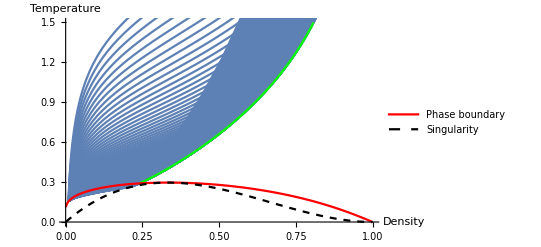

Initial point: (X_0,T_0)=(0.01,0.156543)

Angle range: (Start angle, End angle)=(-π/2,π/2)

Max number of rays: 1000

Actual number of rays: 139

Density of last vapor state on the phase boundary: 0.240318

```mathematica
(*Loading package for extracting domain of DE solutions*)
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"]

(*Defining the temperature T*)
T[t_]:=E^(-Z[t]);

(*Setting initial values*)
Subscript[X, 0]=0.01; (*Initial point of geodesics*)
Subscript[T, 0]=pdTxsmooth[Subscript[X, 0]]; (*Initial point of geodesics*)
StartAngle=-π/2;
EndAngle=π/2;
Rays=1000; (*Number of geodesics from StartAngle to EndAngle*)
EnvelopePoints=100;

(*Solving the geodesic equations*)
solsetvap=
DeleteCases[
Replace[
Reap[
Do[
Sow[
Catch[
NDSolve[{geod1,geod2,X[0]==Subscript[X, 0],Z[0]==-Log[Subscript[T, 0]],X'[0]==Cos[θ],T'[0]==Sin[θ]},{X,Z},{t,0,3},Method->{"EventLocator","Event":>Abs[X'[t]]>100||Abs[Z'[t]]>100,"EventAction":> Throw[Null,"Reject"]}
],
"Reject"
]
],{θ,StartAngle,EndAngle,Abs[EndAngle-StartAngle]/Rays}]][[2,1]],{{x_,y_}}->{x,y},1
],Null
];

(*Generating envelope*)
LastPBVaporState=Xdens/.Table[FindRoot[{solsetvap[[n,1,2]][t]==Xdens,solsetvap[[n,2,2]][t]==-Log[pdTxsmooth[Xdens]]},{{t,0.07},{Xdens,0.2}}],{n,1,Length[solsetvap]}]//Max//Quiet;
tValues=
Reap[
Do[
Sow[
Table[
FindRoot[solsetvap[[n,2,2]][t]==-Log[T],{t,0.03}][[1]],
{n,1,Length[solsetvap]}
]
],{T,pdTxsmooth[LastPBVaporState],1.5,(1.5-pdTxsmooth[LastPBVaporState])/(EnvelopePoints-1)}
]
][[2,1]];
xBoundaryPoints=
Table[
Max[
Table[
solsetvap[[n,1,2]][t]/.tValues[[m,n]],{n,1,Length[solsetvap]}
]
],{m,1,Length[tValues]}
];
TBoundaryPoints=Table[T,{T,pdTxsmooth[LastPBVaporState],1.5,(1.5-pdTxsmooth[LastPBVaporState])/(EnvelopePoints-1)}];
xVapBoundary=ListInterpolation[xBoundaryPoints];
TVapBoundary=ListInterpolation[TBoundaryPoints];

(*Plotting solutions*)
Print["T vs. x"]
Table[ParametricPlot[{X[t]/.solsetvap[[i,1]],E^(-Z[t])/.solsetvap[[i,2]]},{t,0.0001,3},PlotRange->{{0,1},{0,1.5}}],{i,Length[solsetvap]}];
Append[%,ParametricPlot[{xVapBoundary[t],TVapBoundary[t]},{t,InterpolatingFunctionDomain[TVapBoundary][[1,1]],InterpolatingFunctionDomain[TVapBoundary][[1,2]]},PlotStyle->Green]];
Append[%,Plot[{pdTxsmooth[t],2 (-1+t)^2 t},{t,0.001,1},PlotRange->{{0,1},{0,1.5}},PlotStyle->{Red,{Black,Dashed}},PlotLegends->{"Phase boundary","Singularity"}]];
Prepend[%,Plot[0,{x,-2,-1},PlotRange->{{0,1},{0,1.5}},AxesLabel->{"Density","Temperature"}]];
%//Show
Print["Initial point: (X_0,T_0)=","(",Subscript[X, 0],",",Subscript[T, 0],")" ]
Print["Angle range: (Start angle, End angle)=","(",StartAngle,",",EndAngle,")" ]
Print["Max number of rays: ", Rays]
Print["Actual number of rays: ", Length[solsetvap]]
Print["Density of last vapor state on the phase boundary: ",LastPBVaporState]
```

#### Widom line 2 (Maximum CP on isobars)

```mathematica
Temp[p_,x_]=T/.Solve[p==P[T,x],T][[1]];
CP[p_,x_]=T D[P[T,x],T]^2/(D[P[T,x],x]*x^2)/.T->Temp[p,x];
Table[
{x,Temp[p,x]}/.NSolve[D[CP[p,x],x]==0,x][[3]],
{p,1/27+0.01,30/27,0.01}
];
Prepend[%,{1/3,8/27}];
WidomPoints=%;
```

```mathematica
WidomPoints
```

{{1/3,8/27},{0.353533,0.314559},{0.370189,0.330188},{0.384348,0.344005},{0.396648,0.356502},{0.407504,0.367993},{0.417208,0.378695},{0.425968,0.388762},{0.43394,0.398307},{0.441247,0.407416},{0.447981,0.416156},{0.45422,0.424581},{0.460024,0.432732},{0.465446,0.440644},{0.470526,0.448347},{0.475302,0.455865},{0.479804,0.463217},{0.484058,0.47042},{0.488086,0.477491},{0.491909,0.48444},{0.495544,0.49128},{0.499005,0.498021},{0.502308,0.50467},{0.505463,0.511235},{0.508481,0.517723},{0.511373,0.52414},{0.514146,0.530492},{0.516809,0.536782},{0.519369,0.543015},{0.521832,0.549196},{0.524204,0.555328},{0.52649,0.561413},{0.528697,0.567455},{0.530827,0.573457},{0.532885,0.57942},{0.534876,0.585348},{0.536802,0.591242},{0.538668,0.597105},{0.540475,0.602937},{0.542227,0.608741},{0.543927,0.614517},{0.545578,0.620269},{0.54718,0.625996},{0.548737,0.6317},{0.550251,0.637382},{0.551724,0.643043},{0.553157,0.648684},{0.554551,0.654306},{0.55591,0.659911},{0.557233,0.665497},{0.558524,0.671068},{0.559781,0.676622},{0.561009,0.682162},{0.562206,0.687687},{0.563375,0.693198},{0.564516,0.698695},{0.565631,0.70418},{0.56672,0.709653},{0.567784,0.715113},{0.568825,0.720563},{0.569843,0.726001},{0.570839,0.731429},{0.571813,0.736847},{0.572767,0.742255},{0.573701,0.747653},{0.574615,0.753042},{0.575511,0.758423},{0.576389,0.763795},{0.577249,0.769159},{0.578092,0.774515},{0.578918,0.779863},{0.579728,0.785204},{0.580523,0.790538},{0.581303,0.795865},{0.582069,0.801185},{0.58282,0.806499},{0.583557,0.811806},{0.584281,0.817107},{0.584992,0.822403},{0.58569,0.827692},{0.586376,0.832976},{0.58705,0.838255},{0.587713,0.843528},{0.588364,0.848796},{0.589004,0.854059},{0.589633,0.859318},{0.590251,0.864572},{0.59086,0.869821},{0.591459,0.875065},{0.592047,0.880306},{0.592627,0.885542},{0.593197,0.890774},{0.593758,0.896002},{0.59431,0.901227},{0.594854,0.906447},{0.59539,0.911664},{0.595917,0.916877},{0.596436,0.922087},{0.596948,0.927293},{0.597452,0.932496},{0.597948,0.937696},{0.598437,0.942892},{0.598919,0.948086},{0.599394,0.953276},{0.599863,0.958464},{0.600324,0.963648},{0.600779,0.96883},{0.601228,0.974009}}

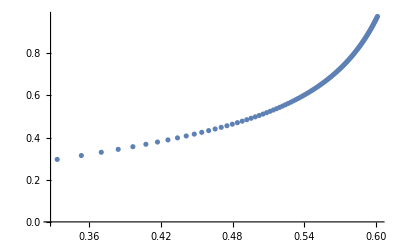

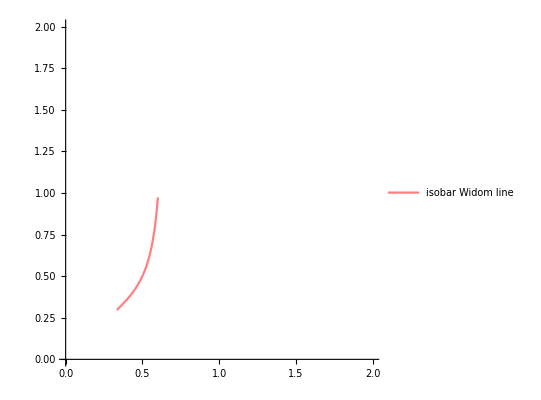

```mathematica
ListPlot[WidomPoints]

(*Smoothing the Widom line*)
ListInterpolation[Table[WidomPoints[[n,2]],{n,1,Length[WidomPoints]}]];
ListInterpolation[Table[WidomPoints[[n,1]],{n,1,Length[WidomPoints]}]];
WidomLineSmooth=ParametricPlot[{%[n],%%[n]},{n,1,Length[WidomPoints]},PlotRange->{{0,2},{0,2}},PlotStyle->{Pink},PlotLegends->{"isobar Widom line"}]
```

#### Widom line*

```mathematica
W[P_]:=(6 P^2 √(3(27+P))+P^2(54+P))^(1/3);
Δ0[T_,P_]:=(P+8T)^2-81P;
Δ1[T_,P_]:=-2(P+8T)^3+243P(P+8T)-729 P^3;
cc[T_,P_]:=(1/2(Δ1[T,P]+√(Δ1[T,P]^2-4 Δ0[T,P]^3)))^(1/3);
TWidomN[P_]:=1/16(-1+P/W[P]+W[P]/P)(P+108(1+P/W[P]+W[P]/P)^-2);
Subscript[v, approx][T_,P_]:=-1/(9P)(-(P+8T)+c[T,P]+Δ0[T,P]/c[T,P]);
PWidomN[T_,x_]:=(8*x*T)/(3-x)-3 x^2;
vWidomN1=Solve[p==PWidomN[TWidomN[p],1/V],V][[1,1,2]];
vWidomN[pr_]:=N[vWidomN1/.p->pr];
TWidom[P_]:=8/27 TWidomN[27P];
PWidom[T_,x_]:=1/27 PWidomN[27/8 T,3x];
vWidom1=Solve[p==PWidom[TWidom[p],1/V],V];
vWidom[pr_]:=N[V/.vWidom1[[1]]/.p->pr];
```

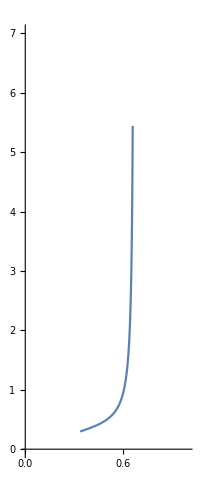

```mathematica
ParametricPlot[{vWidom[P]^-1,TWidom[P]},{P,1/27+0.001,10},PlotRange->{{0,1},{0,7}}]
```

#### Ricci scalar*

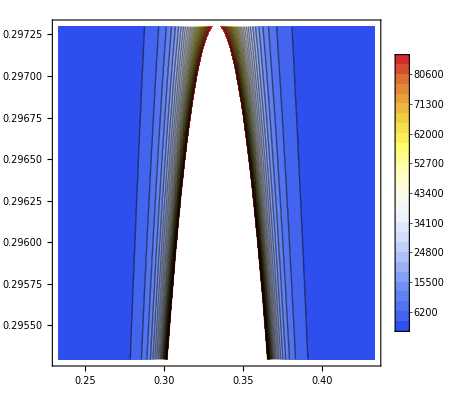

```mathematica
RicciScalarField[X_,t_]:=RicciScalar[CD][[1]]/.{x[]->X,z[]->-Log[t]};
ContourPlot[RicciScalarField[X,T],{X,1/3-0.1,1/3+0.1},{T,8/27-0.001,8/27+0.001},ColorFunction->"TemperatureMap",PlotLegends->Automatic,Contours->100]
```

```mathematica
Manipulate[RicciScalarField[X,pdTxsmooth[X]],{X,0,1}]
```

#### Ricci scalar-based PB*

```mathematica
Clear[Temp]
RicciPBGas[Temp_]:=RicciScalarField[Re[xg/.FindRoot[XGL/.NSolve[Temp==T0,xl][[1]],{xg,0.0001}]],Temp]
RicciPBLiq[Temp_]:=RicciScalarField[Re[xl/.FindRoot[XGL/.NSolve[Temp==T0,xg][[2]],{xl,0.8}]],Temp]
FindRoot[T0==Temp/.xg->%,{xl,0.99}][[1,2]];
%%%-(T0/.{xg->%%,xl->%});
RicciScalarField[{%%%,%%},%%%%];
```

FindRoot::nlnum: The function value {-0.01 (-1.+Null) (0.99+Null)-1. Temp} is not a list of numbers with dimensions {1} at {xl} = {0.99}.

```mathematica
RScalarPBGas=
Reap[
Do[
Sow[
RicciScalarField[Sow[Re[xg/.FindRoot[XGL/.NSolve[Temp==T0,xl][[1]],{xg,0.0001}]],"Density"],Sow[Temp,"Temp"]],"Ricci"],
{Temp,0.01,8/27,0.01}
],
{"Temp","Density","Ricci"}
];
Table[
Max[xl/.NSolve[P[RScalarPBGas[[2,1,1,n]],RScalarPBGas[[2,2,1,n]]]==P[RScalarPBGas[[2,1,1,n]],xl],xl]
],
{n,1,Length[RScalarPBGas[[2,1,1]]]}
];
RPlotGas=
ListInterpolation[RScalarPBGas[[2,3,1]]];
RPlotLiq=
ListInterpolation[
Table[
RicciScalarField[%%[[n]],RScalarPBGas[[2,1,1,n]]],
{n,1,Length[%%]}
]
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

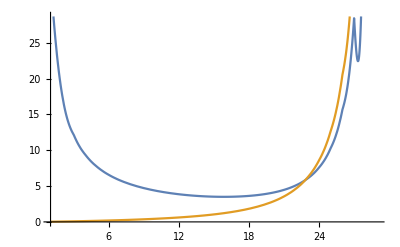

```mathematica
Plot[{RPlotGas[X],RPlotLiq[X]},{X,1,29}]
```

R vs. x

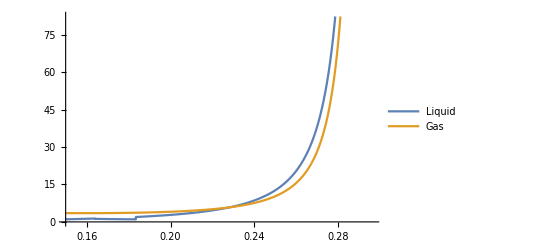

```mathematica
Print["R vs. x"]
Plot[{RicciPBLiq[Temp],RicciPBGas[Temp]},{Temp,0.15,8/27},PlotLegends->{"Liquid","Gas"}]
```

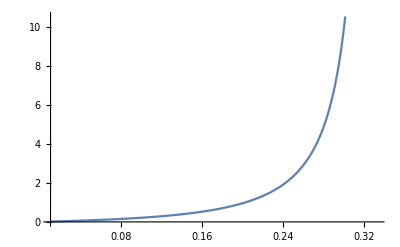

```mathematica
Plot[{RicciScalarField[X,pdTxsmooth[X]]^(1/3) *X},{X,0.01,0.333}]
```

#### Ricci scalar-based Widom line*

```mathematica
Temp[p_,x_]=T/.Solve[p==P[T,x],T][[1]];

WidomRicciPoints=Table[
Re[{X,Temp[p,X]}]/.FindRoot[D[RicciScalarField[X,Temp[p,X]],X]==0,{X,0.33}],
{p,1/27,1,0.001}
]//Quiet;

WidomRicciPlot=ListPlot[WidomRicciPoints,PlotRange->{{0,2},{0,2}},PlotStyle->{Magenta}]
```

FindRoot::nlnum: The function value {(1.34-9.18274 (0.1089+p)) RicciScalarField^(0,1)[0.33,2.0303 (0.1089+p)]+RicciScalarField^(1,0)[0.33,2.0303 (0.1089+p)]} is not a list of numbers with dimensions {1} at {X} = {0.33}.

ReplaceAll::reps: {FindRoot[∂_X RicciScalarField[X,Temp[p,X]]==0,{X,0.33}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(1.34-9.18274 (0.1089+p)) RicciScalarField^(0,1)[0.33,2.0303 (0.1089+p)]+RicciScalarField^(1,0)[0.33,2.0303 (0.1089+p)]} is not a list of numbers with dimensions {1} at {X} = {0.33}.

ReplaceAll::reps: {FindRoot[∂_X RicciScalarField[X,Temp[p,X]]==0,{X,0.33}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(1.34-9.18274 (0.1089+p)) RicciScalarField^(0,1)[0.33,2.0303 (0.1089+p)]+RicciScalarField^(1,0)[0.33,2.0303 (0.1089+p)]} is not a list of numbers with dimensions {1} at {X} = {0.33}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[∂_X RicciScalarField[X,Temp[p,X]]==0,{X,0.33}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {(1.34-9.18274 (0.1089+p)) RicciScalarField^(0,1)[0.33,2.0303 (0.1089+p)]+RicciScalarField^(1,0)[0.33,2.0303 (0.1089+p)]} is not a list of numbers with dimensions {1} at {X} = {0.33}.

ReplaceAll::reps: {FindRoot[∂_X RicciScalarField[X,Temp[p,X]]==0,{X,0.33}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(1.34-9.18274 (0.1089+p)) RicciScalarField^(0,1)[0.33,2.0303 (0.1089+p)]+RicciScalarField^(1,0)[0.33,2.0303 (0.1089+p)]} is not a list of numbers with dimensions {1} at {X} = {0.33}.

ReplaceAll::reps: {FindRoot[∂_X RicciScalarField[X,Temp[p,X]]==0,{X,0.33}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(1.34-9.18274 (0.1089+p)) RicciScalarField^(0,1)[0.33,2.0303 (0.1089+p)]+RicciScalarField^(1,0)[0.33,2.0303 (0.1089+p)]} is not a list of numbers with dimensions {1} at {X} = {0.33}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[∂_X RicciScalarField[X,Temp[p,X]]==0,{X,0.33}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$Aborted

```mathematica
(*Temp[p_,X_]=T/.Solve[p==P[T,X],T][[1]];
MaxRicci=
Table[
ReverseSortBy[
Table[
{p,X,RicciScalarField[X,Temp[p,X]]},
{X,0.001,0.999,0.01}
],Last
][[1]],
{p,1/27,7/27,0.001/3}
];
WidomRicciPlot=
ListPlot[
Table[{MaxRicci[[n,2]],Temp[MaxRicci[[n,1]],MaxRicci[[n,2]]]},{n,1,Length[MaxRicci]}],PlotLegends->{"Ricci-based Widom line"}
]*)
```

#### Summary plot (Run first sections with *)

T vs. x

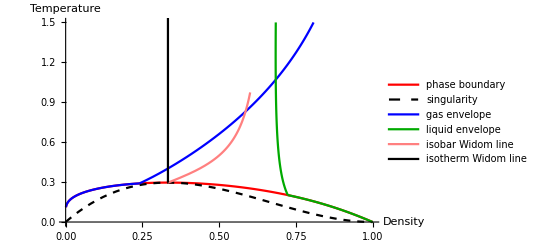

```mathematica
(*Plotting solutions*)
Print["T vs. x"]
{};
(*Table[ParametricPlot[{X[t]/.solset[[i,1]],E^(-Z[t])/.solset[[i,2]]},{t,0.0001,InterpolatingFunctionDomain[solset[[i,1,2]]][[1,2]]},PlotRange->{{0.325,0.335},{0.295,0.3}}],{i,Length[solset]}];*)
Append[%,ParametricPlot[{xVapBoundary[t],TVapBoundary[t]},{t,InterpolatingFunctionDomain[TVapBoundary][[1,1]],InterpolatingFunctionDomain[TVapBoundary][[1,2]]},PlotStyle->Blue,PlotLegends->{"gas envelope"}]];
Append[%,ParametricPlot[{xLiqBoundary[t],TLiqBoundary[t]},{t,InterpolatingFunctionDomain[TLiqBoundary][[1,1]],InterpolatingFunctionDomain[TLiqBoundary][[1,2]]},PlotStyle->Darker[Green],PlotLegends->{"liquid envelope"}]];
Prepend[%,Plot[{pdTxsmooth[t],2 (-1+t)^2 t},{t,0.001,1},PlotStyle->{Red,{Black,Dashed}},PlotLegends->{"phase boundary","singularity"},PlotRange->{{0,1},{0,1.5}},AxesLabel->{"Density","Temperature"}]];
(*Prepend[%,ContourPlot[RicciScalarField[X,T],{X,0,1},{T,0,2},ColorFunction->"TemperatureMap",PlotLegends->Automatic,Contours->50,PlotRange->{{0,1},{0,1}},AxesLabel->{T,x}]];*)
(*Append[%,WidomRicciPlot];*)
Append[%,WidomLineSmooth];
Append[%,Plot[pdTxsmooth[t],{t,0.001,LastPBVaporState},PlotRange->{{0,1},{0,2}},PlotStyle->Blue]];
Append[%,Plot[pdTxsmooth[t],{t,LastPBLiquidState,1},PlotRange->{{0,1.5},{0,1.5}},PlotStyle->Darker[Green]]];
Append[%,ParametricPlot[{1/3,t},{t,8/27,2},PlotStyle->{Thick,Black},PlotLegends->{"isotherm Widom line"},PlotRange->{{0,1},{0,1.5}}]];
(*Append[%,Table[ParametricPlot[{X[t]/.solset1[[i,1]],E^(-Z[t])/.solset1[[i,2]]},{t,0.0001,InterpolatingFunctionDomain[solset1[[i,1,2]]][[1,2]]},PlotRange->{{0.325,0.335},{0.295,0.3}}],{i,Length[solset1]}]];*)
(*Append[%,ParametricPlot[{vWidom[P]^-1,TWidom[P]},{P,1/27+0.001,10},PlotRange->{{0,1},{0,7}},PlotStyle->{Orange},PlotLegends->{"Widom line"},AxesLabel->{T,x}]];*)
%//Show
```

```mathematica
pdTxsmooth[0.98]
```

0.0196

```mathematica
{3/2 x[],1/(x[] (1-x[])^2)-2 E^z[]}/.{x[]->X,z[]->-Log[T]};
{(3 X)/2,-2/T+1/((1-X)^2 X)}/.{X->3X,T->27T/8}
{%[[1]]*(8/27)^2,%[[2]](3)^2}
```

{(9 X)/2,-16/(27 T)+1/(3 (1-3 X)^2 X)}

{(32 X)/81,9 (-16/(27 T)+1/(3 (1-3 X)^2 X))}